## Normal Distribution Mean and Variance Test

### Z-Test H0: μ=μ_0, H1: |μ-μ_0|>= δ

2.74

1.95996

| Statistic | P-Value
Z | 2.74 | 0.00614392

3.16228

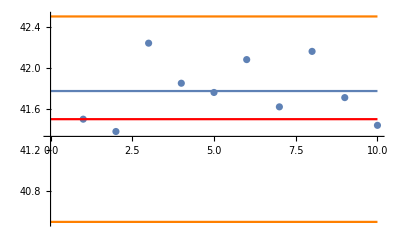

```mathematica
Subscript[μ, 0]:=41.5;δ=1; alpha = 0.05;
data:={41.50,41.38,42.24,41.85,41.76,42.08,41.62,42.16,41.71,41.44};
σ:=√0.1;
x:=Mean[data];n:=Length[data];
Z=(x-Subscript[μ, 0])/(σ/√n)
InverseCDF[NormalDistribution[], 1-alpha/2]
ZTest[data,0.1,41.5,"TestDataTable",AlternativeHypothesis->"Unequal"]
d  = δ/σ
Show[ListPlot[data], Plot[Mean[data],{x,0,n}],Plot[Subscript[μ, 0],{x,0,n}, PlotStyle->Red], Plot[{Subscript[μ, 0]+δ,Subscript[μ, 0]-δ},{x,0,n},PlotStyle->Orange],PlotRange-> All]
```

### Z-Test H0: μ>μ_0, H1: μ<μ_1

2.74

1.64485

| Statistic | P-Value
Z | 2.74 | 0.00307196

3.16228

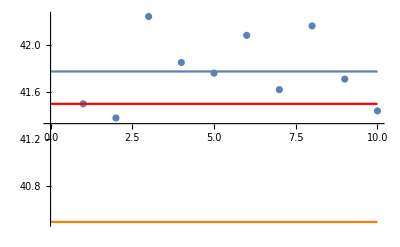

```mathematica
Subscript[μ, 0]:=41.5;Subscript[μ, 1]:= 40.5;alpha = 0.05;
data:={41.50,41.38,42.24,41.85,41.76,42.08,41.62,42.16,41.71,41.44};
σ:=√0.1;
x:=Mean[data];n:=Length[data];
Z=(x-Subscript[μ, 0])/(σ/√n)
InverseCDF[NormalDistribution[], 1-alpha]
ZTest[data,0.1,41.5,"TestDataTable",AlternativeHypothesis->"Greater"]
d  = δ/σ
Show[ListPlot[data], Plot[Mean[data],{x,0,10}],Plot[Subscript[μ, 0],{x,0,10}, PlotStyle->Red], Plot[Subscript[μ, 1],{x,0,10}, PlotStyle->Orange],PlotRange-> All]
```

### T-Test

```mathematica
α=0.05; (*=0.025 a/2 if two sided*)
Subscript[μ, 0]=41.50;Subscript[μ, 1]=40.50;
data:={41.50,41.38,42.24,41.85,41.76,42.08,41.62,42.16,41.71,41.44};

mean=Mean[data];
s2 = Variance[data];
s=√s2;

n=Length[data];
T=(mean-Subscript[μ, 0])/(s/√n)
InverseCDF[StudentTDistribution[n-1],1-α]
d = (Subscript[μ, 0]-Subscript[μ, 1])/s
```

2.8439

1.83311

3.28219

### Chi Squared Test

16.7758

{{8.90652,32.8523},30.1435,10.117}

| Statistic | P-Value
Fisher Ratio | 16.7758 | 0.789889

| Statistic | P-Value
Fisher Ratio | 16.7758 | 0.605055

| Statistic | P-Value
Fisher Ratio | 16.7758 | 0.394945

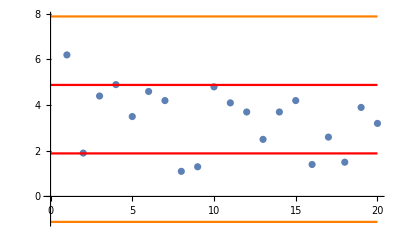

0.8

```mathematica
Subscript[σ, 0]=1.5;alpha = 0.05;
data = {6.2, 1.9, 4.4, 4.9, 3.5,4.6, 4.2, 1.1, 1.3, 4.8,4.1, 3.7, 2.5, 3.7, 4.2,1.4, 2.6, 1.5, 3.9, 3.2};
n=Length[data];
S=√Variance[data];

χ=√(((n-1)S^2)/Subscript[σ, 0]^2);
χ^2
{{InverseCDF[ChiSquareDistribution[n-1],alpha/2],InverseCDF[ChiSquareDistribution[n-1],1-alpha/2]},
InverseCDF[ChiSquareDistribution[n-1],1-alpha],
InverseCDF[ChiSquareDistribution[n-1],alpha]}
FisherRatioTest[data,Subscript[σ, 0]^2,"TestDataTable",AlternativeHypothesis->"Unequal"]
FisherRatioTest[data,Subscript[σ, 0]^2,"TestDataTable",AlternativeHypothesis->"Greater"]
FisherRatioTest[data,Subscript[σ, 0]^2,"TestDataTable",AlternativeHypothesis->"Less"]
Show[ListPlot[data], Plot[{Mean[data]+Subscript[σ, 0],Mean[data]-Subscript[σ, 0]},{x, 0,n}, PlotStyle->Red], Plot[{Mean[data]+3*Subscript[σ, 0],Mean[data]-3*Subscript[σ, 0]},{x, 0,n}, PlotStyle->Orange], PlotRange-> All]
sigma = 1.2;
lambda = sigma/Subscript[σ, 0]
```

## Non-Parametric Single Sample Tests for Median

### Sign Test

```mathematica
data={0,1,2,3,4,5};
q2=1;
SignTest[data,q2,"TestDataTable",AlternativeHypothesis->"Unequal"]
```

| Statistic | P-Value
Sign | 4 | 0.375

### Wilcoxon Signed Rank Test

```mathematica
data={0,1,2,3,4,5};
q2=1;
SignedRankTest[data,q2,"TestDataTable",AlternativeHypothesis->"Unequal"]
```

| Statistic | P-Value
Signed-Rank | 13.5 | 0.136217

## Test for Proportion

### Hypothesis Testing

```mathematica
(*data=;Subscript[p, 0]=;*)
p=Mean[data];
n=Length[data];
Z=(p-Subscript[p, 0])/(√(Subscript[p, 0](1-Subscript[p, 0])/n))
```

### Hypothesis Comparison

```mathematica
(*p1=(*Mean[data1]*);
p2=(*Mean[data2]*);
n1=(*Length[data1]*);
n2=(*Length[data2]*);
d=;*)
Z=(p1-p2-d)/(√((p1(1-p1))/n1+(p2(1-p2))/n2))
```